This notebook is a supplementary realization/simulation of the 1D example provided in the IROS Paper Mapping, “Foraging, and Coverage with a Particle Swarm Controlled by Uniform Inputs” to be published in IROS 2017. More specifically, it addresses the optimality and competitive factor of the bicriteria problem addressed in Section III.A.3. 

For a primer we are assuming that the particle starts on the left side at a distance of d and moves unit distances every step.

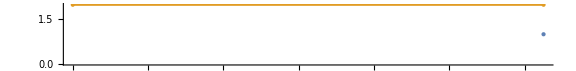

RandomVariate::udist: The specification 2 NormalDistribution[5/2,1/2] is not a random distribution recognized by the system.

RandomVariate::nonopt: Options expected (instead of 6) beyond position 2 in RandomVariate[0,2 NormalDistribution[5/2,1/2],6]. An option must be a rule or a list of rules.

RandomVariate::udist: The specification 2 NormalDistribution[5/2,1/2] is not a random distribution recognized by the system.

RandomVariate::nonopt: Options expected (instead of 6) beyond position 2 in RandomVariate[0,2 NormalDistribution[5/2,1/2],6]. An option must be a rule or a list of rules.

RandomVariate::udist: The specification 2 NormalDistribution[5/2,1/2] is not a random distribution recognized by the system.

General::stop: Further output of RandomVariate::udist will be suppressed during this calculation.

RandomVariate::nonopt: Options expected (instead of 6) beyond position 2 in RandomVariate[0,2 NormalDistribution[5/2,1/2],6]. An option must be a rule or a list of rules.

General::stop: Further output of RandomVariate::nonopt will be suppressed during this calculation.

-Graphics-

```mathematica
move=0; scan=0;d=5;
NumberLinePlot[{d, Interval[{0,d}]},ImageSize->Large]
(*Text["1D Scanning and Mapping"]
Plot[Log{x,x},{x,0, 2d}]*)

moves=RandomVariate[NormalDistribution[d/2,1],20];
scans=RandomVariate[NormalDistribution[d/2,1],20];
(*ListPlot[moves,PlotLabel->"Moves"]
ListPlot[scans, PlotLabel->"Scans"]*)

MRICost[n_]:=Accumulate[Prepend[RandomVariate[NormalDistribution[d/2,d/10]]+RandomVariate[NormalDistribution[d/2,d/10]],n], 0]]
ListLinePlot[Table[MRICost[6],{100}]]
```